```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];
Needs["KerrQNM`"]
SetSpinWeight[-2]
```

All KerrMode routines (QNM) set for Spin-Weight s = -2

```mathematica
SchQNMTable[2]=2;
SchQNMTable[2,0]={0.37-0.09*I,0,0,0,0};
SchQNMTable[2,1]={0.35-0.27*I,0,0,0,0};
SchQNMTable[3]=2;
SchQNMTable[3,0]={0.6-0.09*I,0,0,0,0};
SchQNMTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
SchwarzschildQNM[2,0,RadialDebug->0]
```

Computing (l=2,n=0)

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =1.22354203912149012874092×10^-23 )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

Debug : Got here !

WARNING: cfpow>-1/2 (diff =0. , diffh =0. )

Debug : Starting!

$Aborted

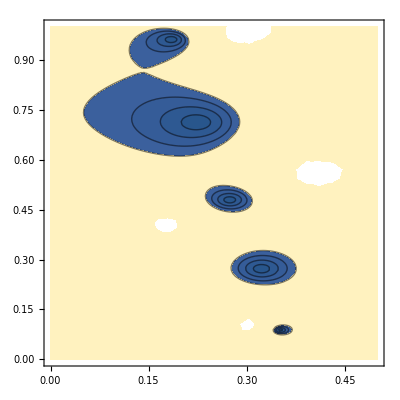

```mathematica
ContourPlot[Abs[PlotContFrac2[2,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],{ωr,0,0.5},{ωi,0,1},Contours->{0,0.5,1,1.5,2}]
```

```mathematica
PlotContFrac[4000,-2,-1,1/2,4,1.1-ⅈ 2.1,3000,15]
```

KerrModes`Private`RadialCFRem::inversion: inversion greater than CF depth

$Aborted

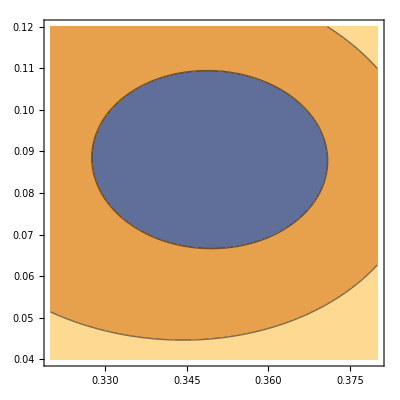

```mathematica
ContourPlot[Abs[PlotContFrac[0,-2,-1,1/2,4,ωr-ⅈ ωi,3000,15]],{ωr,0.32,0.38},{ωi,0.04,0.12},Contours->{0,0.5,1,1.5,2}]
```

```mathematica
?SetSpinWeight
```

SetSpinWeight[s] sets the value of the spin-weight used in all subsequent QNM computations:
	 s=-2 : Gravitational perturbations
	 s=-1 : Electro-Magnetic perturbations
	 s= 0 : Scalar perturbations.

```mathematica
?SchwarzschildQNM
```

SchwarzschildQNM[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrQNM
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.

```mathematica
SchwarzschildQNM[2,0,RadialDebug->2]
```

OptionValue::nodef: Unknown option RadialDebug for SchwarzschildQNM.

OptionValue::optnf: Option name KerrModes`SpinWeight not found in defaults for SchwarzschildQNM.

OptionValue::nodef: Unknown option RadialDebug for SchwarzschildQNM.

OptionValue::optnf: Option name KerrModes`SpinWeight not found in defaults for SchwarzschildQNM.

```mathematica
SchwarzschildQNM[2,1]
```

Computing (l=2,n=1)

{0.346710996879163439717682-0.273914875291234817349552 ⅈ,1,300,-14,4.48374762459683541288732×10^-25}

```mathematica
SchwarzschildQNM[2,7]
```

Computing (l=2,n=2)

{0.301053454612366393018274-0.478276983223071810309085 ⅈ,2,300,-14,3.50976556069590924301404×10^-22}

Computing (l=2,n=3)

{0.251504962185592727495627-0.705148202433494339225473 ⅈ,3,300,-14,1.25435674941828175999762×10^-21}

Computing (l=2,n=4)

{0.207514579813071145491489-0.94684489086635324785649 ⅈ,4,439,-14,3.01771376343677999791552×10^-23}

Computing (l=2,n=5)

{0.169299403093045027411766-1.19560805413584790277213 ⅈ,5,723,-14,3.30382930493256220221089×10^-22}

Computing (l=2,n=6)

{0.133252340245188029172137-1.44791062616203705106769 ⅈ,6,1086,-14,3.12952152582417793221155×10^-21}

Computing (l=2,n=7)

{0.0928223336702009513531975-1.70384117220613551866982 ⅈ,7,3480,-14,2.31281200307829666370081×10^-18}

```mathematica
SchwarzschildQNM[3,0]
```

Computing (l=3,n=0)

{0.599443288437490072739494-0.0927030479449476039700741 ⅈ,0,300,-14,3.15217925795790847916052×10^-21}

```mathematica
SchwarzschildQNM[3,1]
```

Computing (l=3,n=1)

{0.582643803033299430615841-0.281298113435044044678838 ⅈ,1,300,-14,8.68558004758644884622421×10^-23}

```mathematica
SchwarzschildQNM[4,0]
```

Computing (l=4,n=0)

{0.809178377532239140693789-0.0941639609889232494057998 ⅈ,0,300,-14,1.53319546663800061559209×10^-23}

```mathematica
SchwarzschildQNM[4,1,RadialDebug->0]
```

Computing (l=4,n=1)

{0.796631532034502515160255-0.284334349404840718645842 ⅈ,1,300,-14,9.54824053299968525177899×10^-23}

```mathematica
SchwarzschildQNM[5,0]
```

Computing (l=5,n=0)

{1.0122953121353505008792-0.0948705160816095119808521 ⅈ,0,300,-14,3.06264856995914149615042×10^-21}

```mathematica
SchwarzschildQNM[5,1]
```

Computing (l=5,n=1)

{1.00222102789055837442425-0.285817381772263060312771 ⅈ,1,300,-14,7.0439156256414365508779×10^-22}

```mathematica
SchwarzschildQNM[6,4]
```

Computing (l=6,n=0)

{1.21200982065213049039679-0.0952658458420820524539497 ⅈ,0,300,-14,7.2935798708806582246754×10^-22}

Computing (l=6,n=1)

{1.20357397438875375503625-0.286649925113746968634646 ⅈ,1,300,-14,8.67574932358382723522401×10^-23}

Computing (l=6,n=2)

{1.18707367460215801956317-0.480564492780835274634178 ⅈ,2,300,-14,1.63927530443594289512448×10^-22}

Computing (l=6,n=3)

{1.16327006185105959322991-0.678590980982515134928399 ⅈ,3,300,-14,1.50673135228581770781788×10^-23}

Computing (l=6,n=4)

{1.13332410147259103240849-0.882102771131654187186261 ⅈ,4,300,-14,0}

```mathematica
?PlotSchQNM
```

PlotSchQNM[l] plots both the "positive" and "negative" frequency QNMs.  By default, the gravitational modes are plotted, but the PlotSpinWeight option can be set to change this.

Options:
	 PlotSpinWeight->-2 : -2,-1,0

PlotSchQNM also take all of the options available to ListPlot.

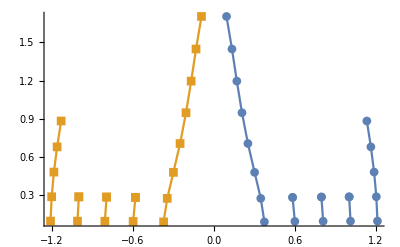

```mathematica
Show[Table[PlotSchQNM[l],{l,2,6}],PlotRange->All]
```

```mathematica
?SchQNMTable
```

Global`SchQNMTable

SchQNMTable[2]=8
 
SchQNMTable[3]=2
 
SchQNMTable[4]=2
 
SchQNMTable[5]=2
 
SchQNMTable[6]=5
 
SchQNMTable[2,0]={0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,9.75515457051863827731063×10^-21}
 
SchQNMTable[2,1]={0.346710996879163439717682-0.273914875291234817349552 ⅈ,1,300,-14,4.48374762459683541288732×10^-25}
 
SchQNMTable[2,2]={0.301053454612366393018274-0.478276983223071810309085 ⅈ,2,300,-14,3.50976556069590924301404×10^-22}
 
SchQNMTable[2,3]={0.251504962185592727495627-0.705148202433494339225473 ⅈ,3,300,-14,1.25435674941828175999762×10^-21}
 
SchQNMTable[2,4]={0.207514579813071145491489-0.94684489086635324785649 ⅈ,4,439,-14,3.01771376343677999791552×10^-23}
 
SchQNMTable[2,5]={0.169299403093045027411766-1.19560805413584790277213 ⅈ,5,723,-14,3.30382930493256220221089×10^-22}
 
SchQNMTable[2,6]={0.133252340245188029172137-1.44791062616203705106769 ⅈ,6,1086,-14,3.12952152582417793221155×10^-21}
 
SchQNMTable[2,7]={0.0928223336702009513531975-1.70384117220613551866982 ⅈ,7,3480,-14,2.31281200307829666370081×10^-18}
 
SchQNMTable[3,0]={0.599443288437490072739494-0.0927030479449476039700741 ⅈ,0,300,-14,3.15217925795790847916052×10^-21}
 
SchQNMTable[3,1]={0.582643803033299430615841-0.281298113435044044678838 ⅈ,1,300,-14,8.68558004758644884622421×10^-23}
 
SchQNMTable[4,0]={0.809178377532239140693789-0.0941639609889232494057998 ⅈ,0,300,-14,1.53319546663800061559209×10^-23}
 
SchQNMTable[4,1]={0.796631532034502515160255-0.284334349404840718645842 ⅈ,1,300,-14,9.54824053299968525177899×10^-23}
 
SchQNMTable[5,0]={1.0122953121353505008792-0.0948705160816095119808521 ⅈ,0,300,-14,3.06264856995914149615042×10^-21}
 
SchQNMTable[5,1]={1.00222102789055837442425-0.285817381772263060312771 ⅈ,1,300,-14,7.0439156256414365508779×10^-22}
 
SchQNMTable[6,0]={1.21200982065213049039679-0.0952658458420820524539497 ⅈ,0,300,-14,7.2935798708806582246754×10^-22}
 
SchQNMTable[6,1]={1.20357397438875375503625-0.286649925113746968634646 ⅈ,1,300,-14,8.67574932358382723522401×10^-23}
 
SchQNMTable[6,2]={1.18707367460215801956317-0.480564492780835274634178 ⅈ,2,300,-14,1.63927530443594289512448×10^-22}
 
SchQNMTable[6,3]={1.16327006185105959322991-0.678590980982515134928399 ⅈ,3,300,-14,1.50673135228581770781788×10^-23}
 
SchQNMTable[6,4]={1.13332410147259103240849-0.882102771131654187186261 ⅈ,4,300,-14,0}